# ComplexArrayPlot

Generates a plot in which the complex values in an array are shown in a discrete array of squares.

## DefinitionDefinitionDefine your function using the name above. All definitions, including dependencies, will be included in the resource function when it is generated. Additional cells can be added and definitions can be given for multiple input cases. This section should be evaluated before evaluating creating the Examples section below.

```mathematica
getColour[com_]:= RGBColor[N[Re[com],10],0,N[Im[com],10]]/;Re[com]≥ 0&&Im[com]≥0
getColour[com_]:= Blend[{ColorNegate[RGBColor[Abs[N[Re[com],10]],0,0]],RGBColor[0,0,N[Im[com],10]]}]/;Re[com]≤ 0&&Im[com]≥0
getColour[com_]:= Blend[{RGBColor[Abs[N[Re[com],10]],0,0],ColorNegate[RGBColor[0,0,N[Im[com],10]]]}]/;Re[com]≥ 0&&Im[com]≤0
getColour[com_]:= Blend[{ColorNegate[RGBColor[Abs[N[Re[com],10]],0,0]],ColorNegate[RGBColor[0,0,N[Im[com],10]]]}]/;Re[com]≤ 0&&Im[com]≤0
```

```mathematica
colourOne[list_]:= getColour[list⟦#⟧]&/@Range[Length[list]]
```

```mathematica
ComplexArrayPlot[array_]:=ArrayPlot[Map[colourNQubit, array]]
```

## Documentation

### UsageUsageDocument every accepted input usage case. Use Enter to create new cases as needed. Each usage should contain a brief explanation saying what the function does for the given input structure. See existing documentation pages for examples.

ComplexArrayPlot[array]

Takes in a 2D array of complex numbers with real and imaginary parts between -1 and 1 and returns an array plot.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used. Add multiple cells including tables and hyperlinks as needed. Typical information includes: acceptable inputs, result formats, options specifications, and background information.

Additional information about usage and options.

## ExamplesExamplesDemonstrate how to use the function. Examples should start with the most basic use case. Each example should be described using text cells. Use "Subsection" and "Subsubsection" cells to group examples as needed. See existing documentation pages for examples.

### Basic Examples

Plot an array:

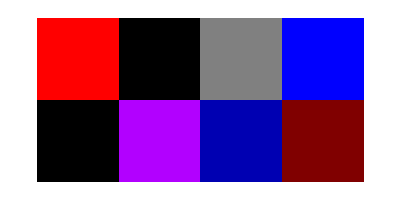

```mathematica
ComplexArrayPlot[{{1,0,-I,I},{0,0.7+I,0.7I,0.5}}]
```

## Source & Additional Information

### Contributed ByContributed ByName of the person, people or organization that should be publicly credited with contributing the function.

Ruhi Shah

### KeywordsKeywordsList relevant terms that should be used to include this resource in search results.

keyword 1

### Related SymbolsRelated SymbolsList related Wolfram Language symbols. Include up to twenty documented, system-level symbols.

SymbolName (documented Wolfram Language symbol)

### Related Resource ObjectsRelated Resource ObjectsNames of published resource objects from any Wolfram repository that are related to this resource.

Resource Name (resources from any Wolfram repository)

### Source/Reference CitationSource/Reference CitationCitation for original source of the function or its components. For example, original publication of an algorithm or public code repository.

Source, reference or citation information

### LinksLinksURLs or hyperlinks for external information related to the function.

Link to other related material

### TestsTestsOptional list of tests that can be used to verify that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as literal VerificationTest expressions if you need to specify options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.